```mathematica
(*待插值函数*)
f1x=Abs[Sin[6 x]]^3-Cos[5 E^x];
f2x=1/(1+25 x^2)-Sin[20 x];
```

```mathematica
(*出于绘图需要，定义函数*)
fx1[x_]:=Sqrt[Sin[6 x]^2]^3-Cos[5 E^x];
fx2[x_]:=1/(1+25 x^2)-Sin[20 x];
```

```mathematica
(*绘制各阶导数，直至出现不连续点*)
```

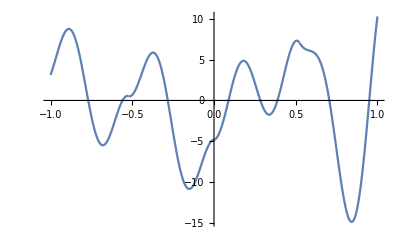
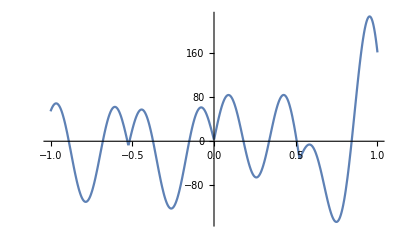
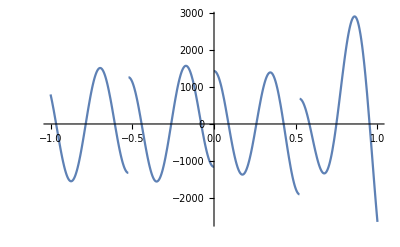

```mathematica
{Plot[Evaluate[D[fx1[x],x]],{x,-1,1}],Plot[Evaluate[D[fx1[x],{x,2}]],{x,-1,1}],Plot[Evaluate[D[fx1[x],{x,3}]],{x,-1,1}]}
```

```mathematica
(*故对于函数1，有连续的2阶导，3阶导不连续，f1的3阶导不是绝对连续，从而m之多最大为3*)
(*而对于函数2，其为[-1,1]上无穷阶连续可导函数，我们不妨取m=3*)
```

```mathematica
(*定义有界变差，将[0,1]区间一千等分，端点函数值插值的绝对值即为有界变差*)
```

```mathematica
boundedvariation[f_]:=Module[{i,n,xn,yn,sum},
n=1000;
xn=(*Table[N[Cos[k Pi/n],50],{k,0,n}];*)Table[N[-1+i 2/n,50],{i,0,n}];
yn=Limit[f,x->xn];
(*yn=f/.x->xn;*)
sum=0;
For[i=2,i≤n+1,i++,sum+=N[Abs[yn[[i]]-yn[[i-1]]],20]];
sum
]
```

```mathematica
(*第一个函数*)
v1=boundedvariation[D[fx1[x],{x,3}]]
```

Indeterminate

```mathematica
(*第二个函数*)
v2=boundedvariation[D[fx2[x],{x,3}]]
```

201542.29167972704291

```mathematica
(*离散傅里叶变换*)
FFT[y_]:=Module[{n,fourier,k,w,min},
n=Length[y];
w=E^(-2 Pi I/n);
fourier=Table[0,{i,1,n}];
For[k=1,k≤n,k++,fourier[[k]]=Sum[y[[j]]*w^((j-1) (k-1)),{j,1,n}]];
fourier
];
```

```mathematica
(*生成Chebyshev多项式*)
Chebyshev[f_,n_]:=Module[{j,y,z,r,px},
(*生成插值节点*)
y=Table[N[Cos[k Pi/n],50],{k,0,n}];
(*拓展节点*)
Do[AppendTo[y,y[[n-i+2]]],{i,2,n}];
(*生成插值节点处函数值*)
z=f/.x->y;
(*傅里叶变换*)
r=Re[FFT[z]];
(*生成Chebyshev插值多项式*)
px=r[[1]]/(2 n);
For[j=2,j≤n,j++,px+=r[[j]]/n *Cos[(j-1)*ArcCos[x]]];(*ChebyshevT[j-1,x]]*)
px+=r[[n+1]]/(2 n) *Cos[n*ArcCos[x]];(*ChebyshevT[n,x]*)
px
];
```

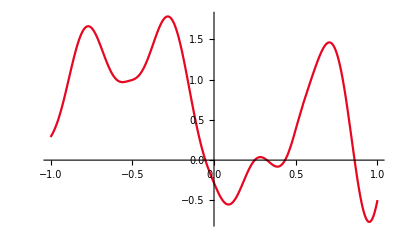
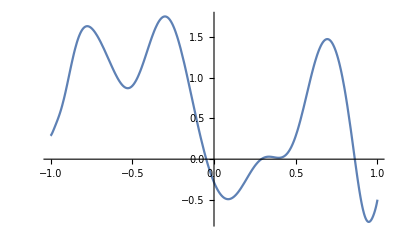
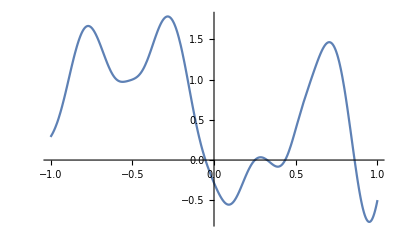
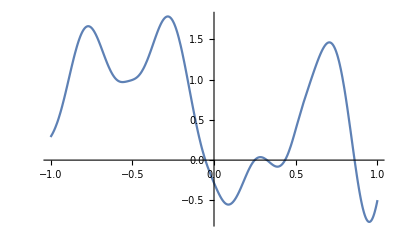
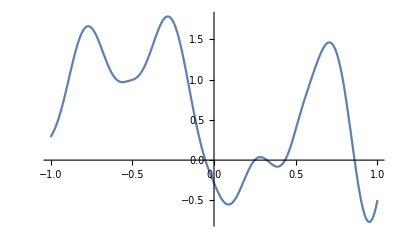

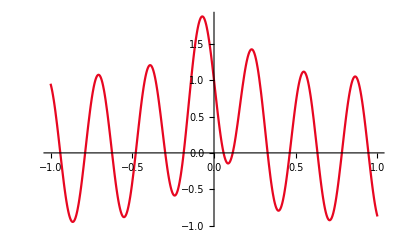
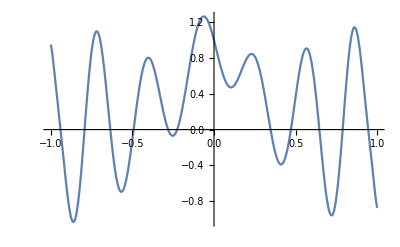
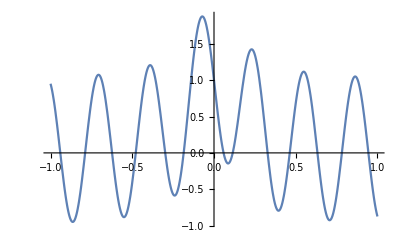

```mathematica
(*生成函数在取20,40,60,80个切比雪夫节点的插值函数图与原图像*)
n={20,40,60,80};img1={Plot[f1x,{x,-1,1},PlotStyle->ColorData[3,"ColorList"]]};
Do[p1x=Chebyshev[f1x,n[[i]]];AppendTo[img1,Plot[p1x,{x,-1,1}]],{i,1,4}]
img2={Plot[f2x,{x,-1,1},PlotStyle->ColorData[3,"ColorList"]]};
Do[p2x=Chebyshev[f2x,n[[i]]];AppendTo[img2,Plot[p2x,{x,-1,1}]],{i,1,4}]
img1
img2
```

```mathematica
(*定义无穷范数，将区间一千等分，考虑等分点处误差绝对值，其中最大者定义为无穷范数作为插值误差*)
 MaxError[f_,px_]:=Module[{n,xn,yn,error},
n=1000;
xn=Table[N[-1+i 2/n,50],{i,0,n}];
yn=Abs[(f-px)/.x->xn];
error=Max[yn]
]
```

```mathematica
(*验证定理二，绘制无穷范数定义的误差在对数坐标下，取节点为1-200，间隔为10，从而生成的图像*)
(*第一个函数*)
```

```mathematica
(*首先生成相应的点图*)
```

```mathematica
errorthm2[f_,v_,m_]:=Module[{error1,p1x,temp},
error1={};
Do[p1x=Chebyshev[f,i];AppendTo[error1,MaxError[f,p1x]],{i,5,100,5}];
temp=Table[4 v/Pi/m/((i-m)^m),{i,5,100,5}];
ListLogLogPlot[{error1,temp}]
]
```

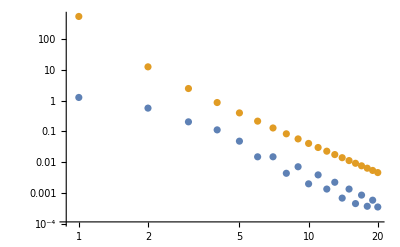

```mathematica
errorthm2[f1x,10000,3]
```

```mathematica
(*首先生成误差*)
```

```mathematica
error1={};
Do[p1x=Chebyshev[f1x,i];AppendTo[error1,{i,MaxError[f1x,p1x]}],{i,1,200,10}];
pic1=ListPlot[Log[error1]];
```

-3.07137764833205382625515010956296703088951

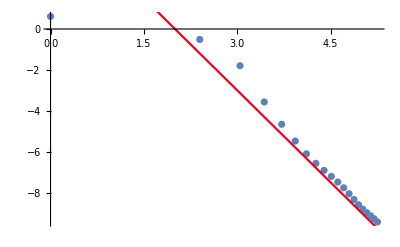

```mathematica
(*计算误差收敛阶*)
k1={};
For[i=4,i<20,i++,AppendTo[k1,(Log[error1[[i+1,2]]]-Log[error1[[i,2]]])/(Log[error1[[i+1,1]]]-Log[error1[[i,1]]])]];
(*输出根据误差计算的斜率的值*)
Mean[k1]
(*绘制所需误差阶图像*)
pic2=Plot[-3 x+6,{x,0,7},PlotStyle->ColorData[3,"ColorList"]];
Show[pic1,pic2]
```

```mathematica
(*由斜率为3此可以看出，对一个函数确实符合m=3*)
```

```mathematica
(*接下来验证n=20,40,60,70的Chebyshev系数的关系*)
```

```mathematica
coeffvariation[f_,v_,m_,n_]:=Module[{i,y,z,r,temp,tempp,pic1,pic2},
(*生成插值节点*)
y=Table[N[Cos[k Pi/n],50],{k,0,n}];
(*拓展节点*)
Do[AppendTo[y,y[[n-i+2]]],{i,2,n}];
(*生成插值节点处函数值*)
z=f/.x->y;
(*傅里叶变换*)
r=Re[FFT[z]];
temp={};
For[i=m+1,i≤n+1,i++,AppendTo[temp,r[[i]]]];
tempp=Table[2 v/Pi/((i-m)^(m+1)),{i,m+1,n+1}];
ListLogLogPlot[{temp,tempp}]
]
```

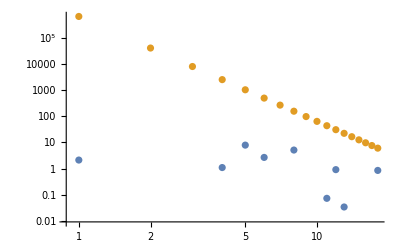
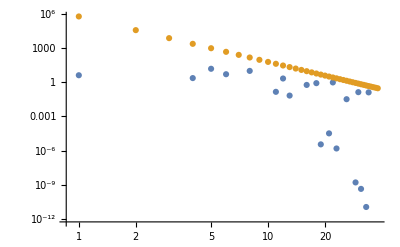
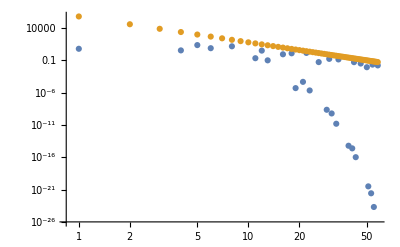
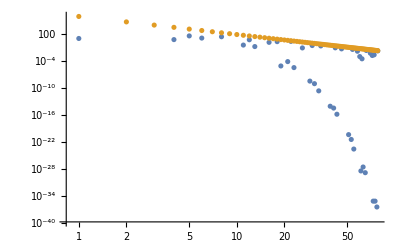

```mathematica
v1=1000000;
{coeffvariation[f1x,v1,3,20],coeffvariation[f1x,v1,3,40],coeffvariation[f1x,v1,3,60],coeffvariation[f1x,v1,3,80]}
```

```mathematica
(*以下为第二个函数验证定理二*)
```

```mathematica
(*生成相应的点图*)
```

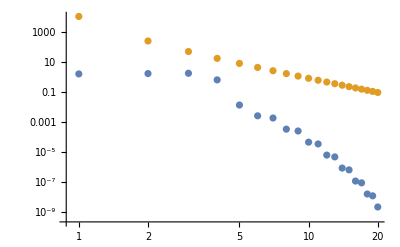

```mathematica
errorthm2[f2x,v2,3]
```

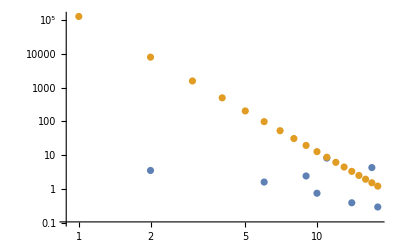
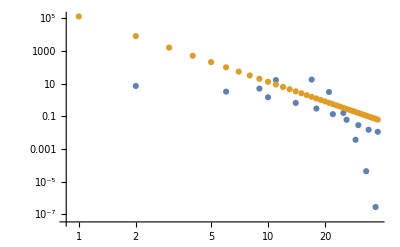
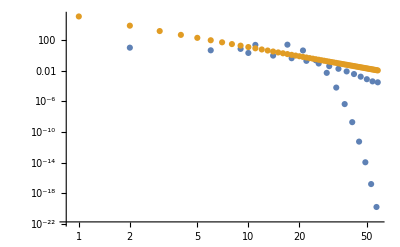
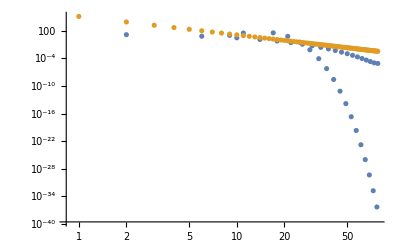

```mathematica
(*接下来验证n=20,40,60,70的Chebyshev系数的关系，需验证其在一条直线上*)
{coeffvariation[f2x,v2,3,20],coeffvariation[f2x,v2,3,40],coeffvariation[f2x,v2,3,60],coeffvariation[f2x,v2,3,80]}
```

```mathematica
(*验证定理三*)
```

```mathematica
(*由于第一个函数在x=0处不解析，故直接验证第二个函数*)
```

```mathematica
(*验证切比雪夫系数不等式*)
```

```mathematica
(*定义求半长轴为a，半短轴为b的椭圆内复变函数的最值*)
```

```mathematica
bound[f_,a_,b_]:=bound[f,a,b]=Module[{m,n,step,theta,result},
step=Table[x,{x,0.01,0.99,0.01}];
theta=Table[x,{x,0,2 Pi,0.02}];
m=Length[step];
n=Length[theta];
result=Table[Norm[f/.x->(step[[i]]*(a*Cos[theta[[j]]]+b*Sin[theta[[j]]]*I))],{i,1,m},{j,1,n}];
Max[result]
]
```

```mathematica
coeffellipse[f_,a_,b_,n_]:=Module[{i,y,z,r,temp,tempp,max},
y=Table[N[Cos[k Pi/n],50],{k,0,n}];(*生成插值节点*)
Do[AppendTo[y,y[[n-i+2]]],{i,2,n}];(*拓展节点*)
z=f/.x->y;(*生成插值节点处函数值*)
r=Re[FFT[z]];(*傅里叶变换*)
temp={};
For[i=1,i≤n+1,i++,AppendTo[temp,Abs[0.01 r[[i]]]]];
max=bound[f,a,b];
tempp=Table[2*max/(a+b)^(i-1),{i,1,n+1}];
ListLogPlot[{temp,tempp}]
]
```

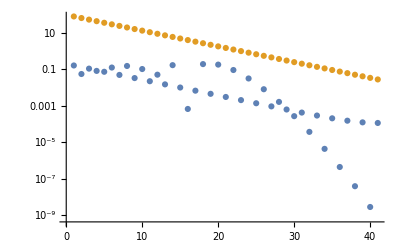

```mathematica
coeffellipse[f2x,Sqrt[1+1/25],1/5,40]
```

```mathematica
(*验证误差的不等式*)
```

```mathematica
errorthm3[f_,a_,b_]:=Module[{error1,p1x,temp,max},
error1={};
Do[p1x=Chebyshev[f,i];AppendTo[error1,MaxError[f,p1x]],{i,5,100,5}];
max=bound[f,a,b];
temp=Table[4*max*(a+b)^(-i)/(a+b-1),{i,5,100,5}];
ListLogPlot[{error1,temp}]
]
```

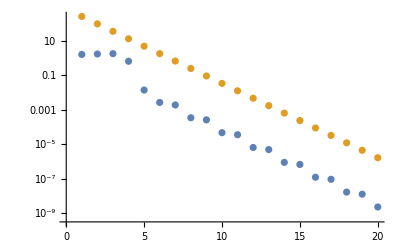

```mathematica
errorthm3[f2x,Sqrt[1+1/25],1/5]
```